```mathematica
Clear["Global`*"]
```

```mathematica
EulerLagrangeEquations[L_,vars_List]:=MapThread[(D[D[L, (D[#, t])], t]==D[L, #])&,{vars}]
RayleighEulerLagrangeEquations[L_,R_,vars_List]:=MapThread[(D[D[L, (D[#, t])], t]+D[R, (D[#, t])]==D[L, #])&,{vars}]
```

```mathematica
SetAttributes[α,Constant]
```

```mathematica
θ[t]:=α;
```

```mathematica
{x[t_],y[t_],z[t_]}:={r[t]Sin[θ[t]]Cos[ϕ[t]],r[t]Sin[θ[t]]Sin[ϕ[t]],r[t]Cos[θ[t]]};
```

```mathematica
v[t]:=D[{x[t],y[t],z[t]},{t}]//FullSimplify
```

```mathematica
L=1/2 m(v[t].v[t])-m g z[t]//FullSimplify
```

1/2 m (-2 g Cos[α] r[t]+r'[t]^2+r[t]^2 Sin[α]^2 ϕ'[t]^2)

```mathematica
R=1/2*β*(v[t].v[t])//Simplify
```

1/2 β (r'[t]^2+r[t]^2 Sin[α]^2 ϕ'[t]^2)

```mathematica
eq0=EulerLagrangeEquations[L,{r[t],ϕ[t]}]
```

{m r''[t]==1/2 m (-2 g Cos[α]+2 r[t] Sin[α]^2 ϕ'[t]^2),2 m r[t] Sin[α]^2 r'[t] ϕ'[t]+m r[t]^2 Sin[α]^2 ϕ''[t]==0}

```mathematica
p=D[L, (D[ϕ[t], t])]
SetAttributes[p,Constant];
```

m r[t]^2 Sin[α]^2 ϕ'[t]

```mathematica
eqs=RayleighEulerLagrangeEquations[L,R,{r[t],ϕ[t]}]
ic={r[0]==(g Cot[α] Csc[α])/ϕ'[0]^2-1,r'[0]==0,ϕ[0]==0,ϕ'[0]==2Pi*0.5};
bdconds={r[t]>=0};
params={α-> Pi/6.,g-> 9.82,m-> 0.2,β->0.02};
```

{β r'[t]+m r''[t]==1/2 m (-2 g Cos[α]+2 r[t] Sin[α]^2 ϕ'[t]^2),β r[t]^2 Sin[α]^2 ϕ'[t]+2 m r[t] Sin[α]^2 r'[t] ϕ'[t]+m r[t]^2 Sin[α]^2 ϕ''[t]==0}

```mathematica
sol=NDSolve[{eq0,ic}/.params//Evaluate,{r[t],ϕ[t]},{t,0,30}]//Flatten;
```

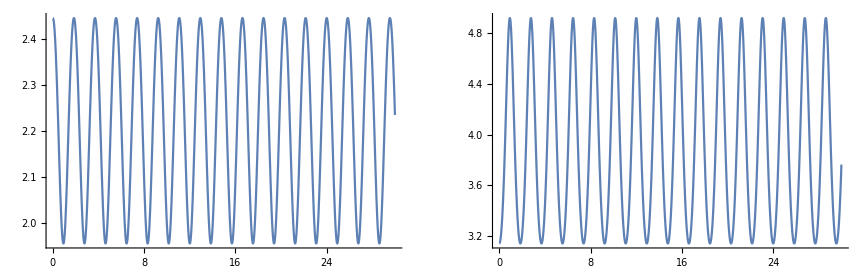

```mathematica
{{Plot[r[t]/.sol,{t,0,30},PlotRange->Full,ImageSize->400],Plot[Evaluate[D[ϕ[t]/.sol,t]],{t,0,30},ImageSize->400]}}//GraphicsGrid
```

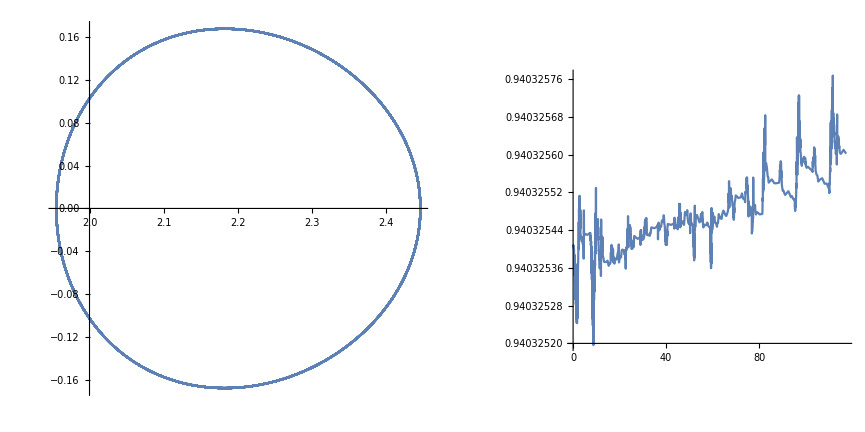

```mathematica
{{ParametricPlot[Evaluate[{r[t]/.sol,m D[(r[t]/.sol), t]}/.params],{t,0,30},ImageSize->400,AspectRatio->1,PlotRange->{Automatic,Automatic}],
ParametricPlot[Evaluate[{ϕ[t],m r[t]^2 Sin[α]^2 D[( ϕ[t]/.sol), t]}/.sol/.params],{t,0,30},ImageSize->300,AspectRatio->1]}}//GraphicsGrid
```

```mathematica
pos[t_]:=Evaluate[{x[t],y[t],z[t]}/.sol/.params]
```

```mathematica
Show[
ParametricPlot3D[pos[t],{t,0,30},ColorFunction->(Hue[1-#4]&),PlotStyle->Directive[Thick]],
ContourPlot3D[
Evaluate[x^2+y^2-(z*Tan[α])^2==0/.params],{x,-20,20},{y,-20,20},{z,-10,100},RegionFunction->(#3==0&)],ImageSize-> 600
]
```

-Graphics3D-